{{0.97,4},{0.98,4},{0.99,4},{1,4},{1.01,4},{1.02,4},{1.03,4},{1.04,4},{1.05,4},{1.06,4},{1.07,4},{1.08,4},{1.09,4},{1.1,4},{1.11,4},{1.12,4},{1.13,4},{1.14,4},{1.15,4},{1.16,4},{1.17,4},{1.18,4},{1.19,4},{1.2,4},{1.21,4},{1.22,4},{1.23,4},{1.24,4},{1.25,4}}

{{1.04,5},{1.05,5},{1.06,5},{1.07,5},{1.08,5},{1.09,5},{1.1,5},{1.11,5},{1.12,5},{1.13,5},{1.14,5},{1.15,5},{1.16,5},{1.17,5},{1.18,5},{1.19,5},{1.2,5}}

{{1.07,6},{1.08,6},{1.09,6},{1.1,6},{1.11,6},{1.12,6},{1.13,6},{1.14,6},{1.15,6},{1.16,6},{1.17,6}}

{{1.1,7},{1.11,7},{1.12,7},{1.13,7},{1.14,7},{1.15,7}}

{{1.11,8},{1.12,8},{1.13,8},{1.14,8}}

{{1.13,9}}

{{1.13,10}}

{{1.11,12},{1.12,12},{1.13,12},{1.14,12},{1.15,12}}

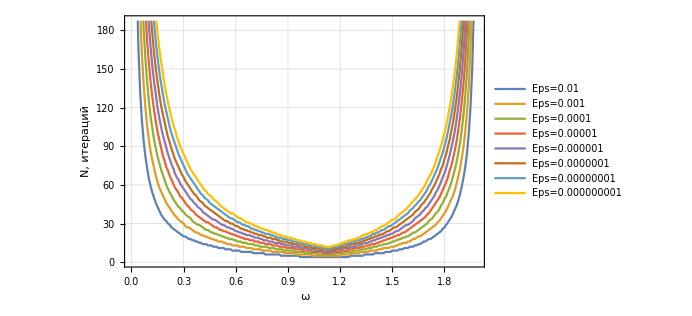

{{0.98,3},{0.99,3},{1.01,3},{1.02,3},{1.04,3},{1.08,3}}

{{0.98,3},{0.99,3},{1.01,3},{1.02,3},{1.03,3}}

{{0.99,3},{1,3},{1.01,3},{1.02,3},{1.03,3}}

{{0.98,3},{1,3},{1.01,3},{1.02,3},{1.04,3}}

{{0.95,4},{0.98,4},{0.99,4},{1,4},{1.01,4},{1.02,4},{1.03,4},{1.04,4},{1.05,4},{1.06,4},{1.07,4}}

{{0.98,4},{0.99,4},{1.02,4},{1.03,4},{1.04,4},{1.05,4},{1.06,4},{1.07,4}}

{{1.01,4},{1.02,4},{1.03,4},{1.04,4},{1.05,4},{1.06,4},{1.07,4},{1.08,4}}

{{1.01,4},{1.02,4},{1.03,4},{1.04,4},{1.06,4}}

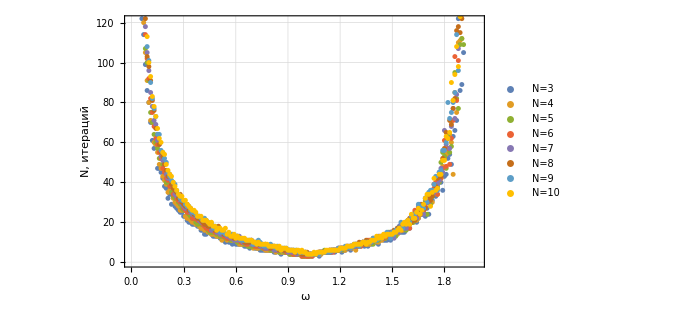

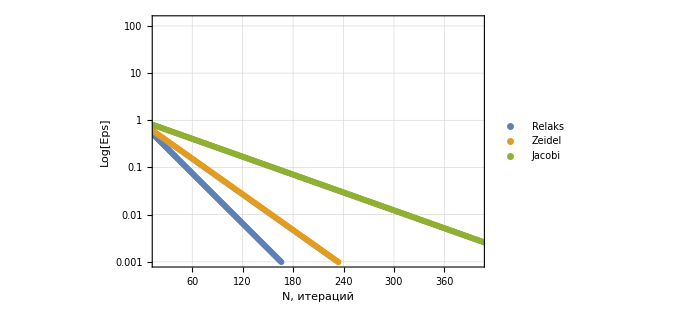

```mathematica
(*Eps=0.01*)dataFind0={{0.01,668},{0.02,333},{0.03,221},{0.04,166},{0.05,132},{0.06,110},{0.07,94},{0.08,82},{0.09,73},{0.1,65},{0.11,59},{0.12,54},{0.13,50},{0.14,46},{0.15,43},{0.16,40},{0.17,37},{0.18,35},{0.19,33},{0.2,32},{0.21,30},{0.22,29},{0.23,27},{0.24,26},{0.25,25},{0.26,24},{0.27,23},{0.28,22},{0.29,21},{0.3,20},{0.31,20},{0.32,19},{0.33,18},{0.34,18},{0.35,17},{0.36,17},{0.37,16},{0.38,16},{0.39,15},{0.4,15},{0.41,14},{0.42,14},{0.43,14},{0.44,13},{0.45,13},{0.46,13},{0.47,12},{0.48,12},{0.49,12},{0.5,11},{0.51,11},{0.52,11},{0.53,11},{0.54,10},{0.55,10},{0.56,10},{0.57,10},{0.58,9},{0.59,9},{0.6,9},{0.61,9},{0.62,9},{0.63,8},{0.64,8},{0.65,8},{0.66,8},{0.67,8},{0.68,8},{0.69,8},{0.7,7},{0.71,7},{0.72,7},{0.73,7},{0.74,7},{0.75,7},{0.76,7},{0.77,6},{0.78,6},{0.79,6},{0.8,6},{0.81,6},{0.82,6},{0.83,6},{0.84,6},{0.85,6},{0.86,5},{0.87,5},{0.88,5},{0.89,5},{0.9,5},{0.91,5},{0.92,5},{0.93,5},{0.94,5},{0.95,5},{0.96,5},{0.97,4},{0.98,4},{0.99,4},{1,4},{1.01,4},{1.02,4},{1.03,4},{1.04,4},{1.05,4},{1.06,4},{1.07,4},{1.08,4},{1.09,4},{1.1,4},{1.11,4},{1.12,4},{1.13,4},{1.14,4},{1.15,4},{1.16,4},{1.17,4},{1.18,4},{1.19,4},{1.2,4},{1.21,4},{1.22,4},{1.23,4},{1.24,4},{1.25,4},{1.26,5},{1.27,5},{1.28,5},{1.29,5},{1.3,5},{1.31,5},{1.32,5},{1.33,5},{1.34,6},{1.35,6},{1.36,6},{1.37,6},{1.38,6},{1.39,6},{1.4,7},{1.41,7},{1.42,7},{1.43,7},{1.44,7},{1.45,7},{1.46,8},{1.47,8},{1.48,8},{1.49,8},{1.5,9},{1.51,9},{1.52,9},{1.53,9},{1.54,10},{1.55,10},{1.56,10},{1.57,11},{1.58,11},{1.59,11},{1.6,12},{1.61,12},{1.62,12},{1.63,13},{1.64,13},{1.65,14},{1.66,14},{1.67,15},{1.68,16},{1.69,16},{1.7,17},{1.71,18},{1.72,18},{1.73,19},{1.74,20},{1.75,21},{1.76,22},{1.77,23},{1.78,24},{1.79,26},{1.8,27},{1.81,29},{1.82,31},{1.83,33},{1.84,35},{1.85,38},{1.86,41},{1.87,44},{1.88,48},{1.89,53},{1.9,59},{1.91,66},{1.92,74},{1.93,85},{1.94,100},{1.95,121},{1.96,151},{1.97,203},{1.98,305},{1.99,613}};
(*Eps=0.001*)
dataFind1={{0.01,982},{0.02,489},{0.03,325},{0.04,243},{0.05,194},{0.06,161},{0.07,138},{0.08,120},{0.09,106},{0.1,95},{0.11,86},{0.12,79},{0.13,73},{0.14,67},{0.15,62},{0.16,58},{0.17,55},{0.18,52},{0.19,49},{0.2,46},{0.21,44},{0.22,42},{0.23,40},{0.24,38},{0.25,36},{0.26,35},{0.27,33},{0.28,32},{0.29,31},{0.3,30},{0.31,28},{0.32,27},{0.33,27},{0.34,26},{0.35,25},{0.36,24},{0.37,23},{0.38,23},{0.39,22},{0.4,21},{0.41,21},{0.42,20},{0.43,20},{0.44,19},{0.45,19},{0.46,18},{0.47,18},{0.48,17},{0.49,17},{0.5,16},{0.51,16},{0.52,16},{0.53,15},{0.54,15},{0.55,14},{0.56,14},{0.57,14},{0.58,13},{0.59,13},{0.6,13},{0.61,13},{0.62,12},{0.63,12},{0.64,12},{0.65,12},{0.66,11},{0.67,11},{0.68,11},{0.69,11},{0.7,10},{0.71,10},{0.72,10},{0.73,10},{0.74,10},{0.75,9},{0.76,9},{0.77,9},{0.78,9},{0.79,9},{0.8,9},{0.81,8},{0.82,8},{0.83,8},{0.84,8},{0.85,8},{0.86,8},{0.87,8},{0.88,7},{0.89,7},{0.9,7},{0.91,7},{0.92,7},{0.93,7},{0.94,7},{0.95,6},{0.96,6},{0.97,6},{0.98,6},{0.99,6},{1,6},{1.01,6},{1.02,6},{1.03,6},{1.04,5},{1.05,5},{1.06,5},{1.07,5},{1.08,5},{1.09,5},{1.1,5},{1.11,5},{1.12,5},{1.13,5},{1.14,5},{1.15,5},{1.16,5},{1.17,5},{1.18,5},{1.19,5},{1.2,5},{1.21,6},{1.22,6},{1.23,6},{1.24,6},{1.25,6},{1.26,6},{1.27,7},{1.28,7},{1.29,7},{1.3,7},{1.31,7},{1.32,8},{1.33,8},{1.34,8},{1.35,8},{1.36,8},{1.37,9},{1.38,9},{1.39,9},{1.4,9},{1.41,9},{1.42,10},{1.43,10},{1.44,10},{1.45,11},{1.46,11},{1.47,11},{1.48,11},{1.49,12},{1.5,12},{1.51,12},{1.52,13},{1.53,13},{1.54,14},{1.55,14},{1.56,15},{1.57,15},{1.58,15},{1.59,16},{1.6,16},{1.61,17},{1.62,18},{1.63,18},{1.64,19},{1.65,20},{1.66,20},{1.67,21},{1.68,22},{1.69,23},{1.7,24},{1.71,25},{1.72,26},{1.73,27},{1.74,28},{1.75,29},{1.76,31},{1.77,32},{1.78,34},{1.79,36},{1.8,38},{1.81,40},{1.82,43},{1.83,46},{1.84,49},{1.85,52},{1.86,56},{1.87,61},{1.88,67},{1.89,73},{1.9,81},{1.91,90},{1.92,102},{1.93,117},{1.94,137},{1.95,165},{1.96,208},{1.97,278},{1.98,419},{1.99,842}};
(*Eps=0.0001*)
dataFind2={{0.01,1291},{0.02,643},{0.03,427},{0.04,319},{0.05,255},{0.06,211},{0.07,181},{0.08,158},{0.09,140},{0.1,125},{0.11,113},{0.12,104},{0.13,95},{0.14,88},{0.15,82},{0.16,77},{0.17,72},{0.18,68},{0.19,64},{0.2,60},{0.21,57},{0.22,54},{0.23,52},{0.24,49},{0.25,47},{0.26,45},{0.27,43},{0.28,42},{0.29,40},{0.3,39},{0.31,37},{0.32,36},{0.33,35},{0.34,34},{0.35,32},{0.36,31},{0.37,30},{0.38,29},{0.39,29},{0.4,28},{0.41,27},{0.42,26},{0.43,25},{0.44,25},{0.45,24},{0.46,23},{0.47,23},{0.48,22},{0.49,22},{0.5,21},{0.51,21},{0.52,20},{0.53,20},{0.54,19},{0.55,19},{0.56,18},{0.57,18},{0.58,18},{0.59,17},{0.6,17},{0.61,16},{0.62,16},{0.63,16},{0.64,15},{0.65,15},{0.66,15},{0.67,14},{0.68,14},{0.69,14},{0.7,14},{0.71,13},{0.72,13},{0.73,13},{0.74,12},{0.75,12},{0.76,12},{0.77,12},{0.78,12},{0.79,11},{0.8,11},{0.81,11},{0.82,11},{0.83,10},{0.84,10},{0.85,10},{0.86,10},{0.87,10},{0.88,9},{0.89,9},{0.9,9},{0.91,9},{0.92,9},{0.93,9},{0.94,8},{0.95,8},{0.96,8},{0.97,8},{0.98,8},{0.99,8},{1,7},{1.01,7},{1.02,7},{1.03,7},{1.04,7},{1.05,7},{1.06,7},{1.07,6},{1.08,6},{1.09,6},{1.1,6},{1.11,6},{1.12,6},{1.13,6},{1.14,6},{1.15,6},{1.16,6},{1.17,6},{1.18,7},{1.19,7},{1.2,7},{1.21,7},{1.22,7},{1.23,8},{1.24,8},{1.25,8},{1.26,8},{1.27,8},{1.28,9},{1.29,9},{1.3,9},{1.31,9},{1.32,10},{1.33,10},{1.34,10},{1.35,10},{1.36,11},{1.37,11},{1.38,11},{1.39,12},{1.4,12},{1.41,12},{1.42,13},{1.43,13},{1.44,13},{1.45,14},{1.46,14},{1.47,14},{1.48,15},{1.49,15},{1.5,16},{1.51,16},{1.52,17},{1.53,17},{1.54,18},{1.55,18},{1.56,19},{1.57,19},{1.58,20},{1.59,20},{1.6,21},{1.61,22},{1.62,23},{1.63,23},{1.64,24},{1.65,25},{1.66,26},{1.67,27},{1.68,28},{1.69,29},{1.7,30},{1.71,32},{1.72,33},{1.73,34},{1.74,36},{1.75,38},{1.76,39},{1.77,41},{1.78,44},{1.79,46},{1.8,49},{1.81,51},{1.82,55},{1.83,58},{1.84,62},{1.85,67},{1.86,72},{1.87,78},{1.88,85},{1.89,93},{1.9,103},{1.91,115},{1.92,130},{1.93,149},{1.94,174},{1.95,210},{1.96,264},{1.97,354},{1.98,533},{1.99,1071}};
(*Eps=1e-05*)
dataFind3={{0.01,1597},{0.02,796},{0.03,529},{0.04,395},{0.05,315},{0.06,262},{0.07,223},{0.08,195},{0.09,172},{0.1,155},{0.11,140},{0.12,128},{0.13,118},{0.14,109},{0.15,101},{0.16,95},{0.17,89},{0.18,83},{0.19,79},{0.2,74},{0.21,71},{0.22,67},{0.23,64},{0.24,61},{0.25,58},{0.26,56},{0.27,54},{0.28,51},{0.29,50},{0.3,48},{0.31,46},{0.32,44},{0.33,43},{0.34,41},{0.35,40},{0.36,39},{0.37,37},{0.38,36},{0.39,35},{0.4,34},{0.41,33},{0.42,32},{0.43,31},{0.44,31},{0.45,30},{0.46,29},{0.47,28},{0.48,27},{0.49,27},{0.5,26},{0.51,25},{0.52,25},{0.53,24},{0.54,24},{0.55,23},{0.56,23},{0.57,22},{0.58,22},{0.59,21},{0.6,21},{0.61,20},{0.62,20},{0.63,19},{0.64,19},{0.65,18},{0.66,18},{0.67,18},{0.68,17},{0.69,17},{0.7,17},{0.71,16},{0.72,16},{0.73,16},{0.74,15},{0.75,15},{0.76,15},{0.77,14},{0.78,14},{0.79,14},{0.8,14},{0.81,13},{0.82,13},{0.83,13},{0.84,13},{0.85,12},{0.86,12},{0.87,12},{0.88,12},{0.89,11},{0.9,11},{0.91,11},{0.92,11},{0.93,11},{0.94,10},{0.95,10},{0.96,10},{0.97,10},{0.98,10},{0.99,9},{1,9},{1.01,9},{1.02,9},{1.03,9},{1.04,8},{1.05,8},{1.06,8},{1.07,8},{1.08,8},{1.09,8},{1.1,7},{1.11,7},{1.12,7},{1.13,7},{1.14,7},{1.15,7},{1.16,8},{1.17,8},{1.18,8},{1.19,8},{1.2,8},{1.21,9},{1.22,9},{1.23,9},{1.24,9},{1.25,10},{1.26,10},{1.27,10},{1.28,11},{1.29,11},{1.3,11},{1.31,11},{1.32,12},{1.33,12},{1.34,12},{1.35,13},{1.36,13},{1.37,13},{1.38,14},{1.39,14},{1.4,14},{1.41,15},{1.42,15},{1.43,16},{1.44,16},{1.45,17},{1.46,17},{1.47,18},{1.48,18},{1.49,19},{1.5,19},{1.51,20},{1.52,20},{1.53,21},{1.54,21},{1.55,22},{1.56,23},{1.57,23},{1.58,24},{1.59,25},{1.6,26},{1.61,27},{1.62,28},{1.63,29},{1.64,30},{1.65,31},{1.66,32},{1.67,33},{1.68,34},{1.69,35},{1.7,37},{1.71,38},{1.72,40},{1.73,42},{1.74,44},{1.75,46},{1.76,48},{1.77,50},{1.78,53},{1.79,56},{1.8,59},{1.81,62},{1.82,66},{1.83,71},{1.84,75},{1.85,81},{1.86,87},{1.87,94},{1.88,103},{1.89,113},{1.9,125},{1.91,139},{1.92,157},{1.93,181},{1.94,212},{1.95,255},{1.96,321},{1.97,429},{1.98,647},{1.99,1301}};
(*Eps=1e-06*)
dataFind4={{0.01,1902},{0.02,948},{0.03,630},{0.04,471},{0.05,375},{0.06,311},{0.07,266},{0.08,232},{0.09,205},{0.1,184},{0.11,167},{0.12,152},{0.13,140},{0.14,130},{0.15,120},{0.16,112},{0.17,105},{0.18,99},{0.19,94},{0.2,89},{0.21,84},{0.22,80},{0.23,76},{0.24,73},{0.25,69},{0.26,66},{0.27,64},{0.28,61},{0.29,59},{0.3,57},{0.31,55},{0.32,53},{0.33,51},{0.34,49},{0.35,48},{0.36,46},{0.37,45},{0.38,43},{0.39,42},{0.4,41},{0.41,39},{0.42,38},{0.43,37},{0.44,36},{0.45,35},{0.46,34},{0.47,33},{0.48,33},{0.49,32},{0.5,31},{0.51,30},{0.52,29},{0.53,29},{0.54,28},{0.55,27},{0.56,27},{0.57,26},{0.58,26},{0.59,25},{0.6,24},{0.61,24},{0.62,23},{0.63,23},{0.64,22},{0.65,22},{0.66,21},{0.67,21},{0.68,21},{0.69,20},{0.7,20},{0.71,19},{0.72,19},{0.73,19},{0.74,18},{0.75,18},{0.76,17},{0.77,17},{0.78,17},{0.79,16},{0.8,16},{0.81,16},{0.82,15},{0.83,15},{0.84,15},{0.85,15},{0.86,14},{0.87,14},{0.88,14},{0.89,13},{0.9,13},{0.91,13},{0.92,13},{0.93,12},{0.94,12},{0.95,12},{0.96,12},{0.97,11},{0.98,11},{0.99,11},{1,11},{1.01,11},{1.02,10},{1.03,10},{1.04,10},{1.05,10},{1.06,9},{1.07,9},{1.08,9},{1.09,9},{1.1,9},{1.11,8},{1.12,8},{1.13,8},{1.14,8},{1.15,9},{1.16,9},{1.17,9},{1.18,9},{1.19,10},{1.2,10},{1.21,10},{1.22,11},{1.23,11},{1.24,11},{1.25,11},{1.26,12},{1.27,12},{1.28,12},{1.29,13},{1.3,13},{1.31,13},{1.32,14},{1.33,14},{1.34,15},{1.35,15},{1.36,15},{1.37,16},{1.38,16},{1.39,17},{1.4,17},{1.41,18},{1.42,18},{1.43,19},{1.44,19},{1.45,20},{1.46,20},{1.47,21},{1.48,21},{1.49,22},{1.5,22},{1.51,23},{1.52,24},{1.53,24},{1.54,25},{1.55,26},{1.56,27},{1.57,28},{1.58,29},{1.59,29},{1.6,30},{1.61,31},{1.62,32},{1.63,34},{1.64,35},{1.65,36},{1.66,37},{1.67,39},{1.68,40},{1.69,42},{1.7,43},{1.71,45},{1.72,47},{1.73,49},{1.74,51},{1.75,54},{1.76,56},{1.77,59},{1.78,62},{1.79,66},{1.8,69},{1.81,73},{1.82,78},{1.83,83},{1.84,89},{1.85,95},{1.86,102},{1.87,111},{1.88,121},{1.89,132},{1.9,146},{1.91,163},{1.92,185},{1.93,212},{1.94,249},{1.95,300},{1.96,377},{1.97,505},{1.98,761},{1.99,1530}};
(*Eps=1e-07*)
dataFind5={{0.01,2207},{0.02,1100},{0.03,731},{0.04,546},{0.05,435},{0.06,361},{0.07,309},{0.08,269},{0.09,238},{0.1,214},{0.11,193},{0.12,177},{0.13,162},{0.14,150},{0.15,140},{0.16,130},{0.17,122},{0.18,115},{0.19,109},{0.2,103},{0.21,97},{0.22,93},{0.23,88},{0.24,84},{0.25,80},{0.26,77},{0.27,74},{0.28,71},{0.29,68},{0.3,66},{0.31,63},{0.32,61},{0.33,59},{0.34,57},{0.35,55},{0.36,53},{0.37,52},{0.38,50},{0.39,48},{0.4,47},{0.41,46},{0.42,44},{0.43,43},{0.44,42},{0.45,41},{0.46,40},{0.47,39},{0.48,38},{0.49,37},{0.5,36},{0.51,35},{0.52,34},{0.53,33},{0.54,32},{0.55,32},{0.56,31},{0.57,30},{0.58,30},{0.59,29},{0.6,28},{0.61,28},{0.62,27},{0.63,26},{0.64,26},{0.65,25},{0.66,25},{0.67,24},{0.68,24},{0.69,23},{0.7,23},{0.71,22},{0.72,22},{0.73,21},{0.74,21},{0.75,21},{0.76,20},{0.77,20},{0.78,19},{0.79,19},{0.8,19},{0.81,18},{0.82,18},{0.83,18},{0.84,17},{0.85,17},{0.86,16},{0.87,16},{0.88,16},{0.89,16},{0.9,15},{0.91,15},{0.92,15},{0.93,14},{0.94,14},{0.95,14},{0.96,13},{0.97,13},{0.98,13},{0.99,13},{1,12},{1.01,12},{1.02,12},{1.03,12},{1.04,11},{1.05,11},{1.06,11},{1.07,11},{1.08,10},{1.09,10},{1.1,10},{1.11,10},{1.12,10},{1.13,9},{1.14,10},{1.15,10},{1.16,10},{1.17,10},{1.18,11},{1.19,11},{1.2,11},{1.21,12},{1.22,12},{1.23,12},{1.24,13},{1.25,13},{1.26,14},{1.27,14},{1.28,14},{1.29,15},{1.3,15},{1.31,15},{1.32,16},{1.33,16},{1.34,17},{1.35,17},{1.36,18},{1.37,18},{1.38,19},{1.39,19},{1.4,20},{1.41,20},{1.42,21},{1.43,21},{1.44,22},{1.45,22},{1.46,23},{1.47,24},{1.48,24},{1.49,25},{1.5,26},{1.51,27},{1.52,27},{1.53,28},{1.54,29},{1.55,30},{1.56,31},{1.57,32},{1.58,33},{1.59,34},{1.6,35},{1.61,36},{1.62,37},{1.63,39},{1.64,40},{1.65,41},{1.66,43},{1.67,45},{1.68,46},{1.69,48},{1.7,50},{1.71,52},{1.72,54},{1.73,57},{1.74,59},{1.75,62},{1.76,65},{1.77,68},{1.78,72},{1.79,75},{1.8,80},{1.81,84},{1.82,90},{1.83,95},{1.84,102},{1.85,109},{1.86,118},{1.87,127},{1.88,139},{1.89,152},{1.9,168},{1.91,188},{1.92,212},{1.93,244},{1.94,286},{1.95,345},{1.96,433},{1.97,581},{1.98,875},{1.99,1759}};
(*Eps=1e-08*)
dataFind6={{0.01,2512},{0.02,1252},{0.03,831},{0.04,621},{0.05,495},{0.06,411},{0.07,351},{0.08,306},{0.09,271},{0.1,243},{0.11,220},{0.12,201},{0.13,185},{0.14,171},{0.15,159},{0.16,148},{0.17,139},{0.18,131},{0.19,123},{0.2,117},{0.21,111},{0.22,105},{0.23,100},{0.24,96},{0.25,92},{0.26,88},{0.27,84},{0.28,81},{0.29,78},{0.3,75},{0.31,72},{0.32,69},{0.33,67},{0.34,65},{0.35,63},{0.36,61},{0.37,59},{0.38,57},{0.39,55},{0.4,53},{0.41,52},{0.42,50},{0.43,49},{0.44,48},{0.45,46},{0.46,45},{0.47,44},{0.48,43},{0.49,42},{0.5,41},{0.51,40},{0.52,39},{0.53,38},{0.54,37},{0.55,36},{0.56,35},{0.57,34},{0.58,34},{0.59,33},{0.6,32},{0.61,31},{0.62,31},{0.63,30},{0.64,29},{0.65,29},{0.66,28},{0.67,28},{0.68,27},{0.69,26},{0.7,26},{0.71,25},{0.72,25},{0.73,24},{0.74,24},{0.75,23},{0.76,23},{0.77,22},{0.78,22},{0.79,22},{0.8,21},{0.81,21},{0.82,20},{0.83,20},{0.84,19},{0.85,19},{0.86,19},{0.87,18},{0.88,18},{0.89,18},{0.9,17},{0.91,17},{0.92,17},{0.93,16},{0.94,16},{0.95,16},{0.96,15},{0.97,15},{0.98,15},{0.99,14},{1,14},{1.01,14},{1.02,13},{1.03,13},{1.04,13},{1.05,13},{1.06,12},{1.07,12},{1.08,12},{1.09,12},{1.1,11},{1.11,11},{1.12,11},{1.13,10},{1.14,11},{1.15,11},{1.16,11},{1.17,12},{1.18,12},{1.19,12},{1.2,13},{1.21,13},{1.22,14},{1.23,14},{1.24,14},{1.25,15},{1.26,15},{1.27,16},{1.28,16},{1.29,17},{1.3,17},{1.31,17},{1.32,18},{1.33,18},{1.34,19},{1.35,19},{1.36,20},{1.37,20},{1.38,21},{1.39,22},{1.4,22},{1.41,23},{1.42,23},{1.43,24},{1.44,25},{1.45,25},{1.46,26},{1.47,27},{1.48,28},{1.49,28},{1.5,29},{1.51,30},{1.52,31},{1.53,32},{1.54,33},{1.55,34},{1.56,35},{1.57,36},{1.58,37},{1.59,38},{1.6,40},{1.61,41},{1.62,42},{1.63,44},{1.64,45},{1.65,47},{1.66,48},{1.67,50},{1.68,52},{1.69,54},{1.7,56},{1.71,59},{1.72,61},{1.73,64},{1.74,67},{1.75,70},{1.76,73},{1.77,77},{1.78,81},{1.79,85},{1.8,90},{1.81,95},{1.82,101},{1.83,108},{1.84,115},{1.85,123},{1.86,133},{1.87,144},{1.88,157},{1.89,172},{1.9,190},{1.91,212},{1.92,240},{1.93,276},{1.94,323},{1.95,390},{1.96,490},{1.97,656},{1.98,989},{1.99,1988}};
(*Eps=1e-09*)
dataFind7={{0.01,2817},{0.02,1403},{0.03,932},{0.04,697},{0.05,555},{0.06,461},{0.07,394},{0.08,343},{0.09,304},{0.1,272},{0.11,247},{0.12,225},{0.13,207},{0.14,192},{0.15,178},{0.16,166},{0.17,156},{0.18,147},{0.19,138},{0.2,131},{0.21,124},{0.22,118},{0.23,112},{0.24,107},{0.25,103},{0.26,98},{0.27,94},{0.28,90},{0.29,87},{0.3,84},{0.31,81},{0.32,78},{0.33,75},{0.34,72},{0.35,70},{0.36,68},{0.37,66},{0.38,64},{0.39,62},{0.4,60},{0.41,58},{0.42,56},{0.43,55},{0.44,53},{0.45,52},{0.46,51},{0.47,49},{0.48,48},{0.49,47},{0.5,46},{0.51,44},{0.52,43},{0.53,42},{0.54,41},{0.55,40},{0.56,39},{0.57,38},{0.58,38},{0.59,37},{0.6,36},{0.61,35},{0.62,34},{0.63,34},{0.64,33},{0.65,32},{0.66,31},{0.67,31},{0.68,30},{0.69,30},{0.7,29},{0.71,28},{0.72,28},{0.73,27},{0.74,27},{0.75,26},{0.76,26},{0.77,25},{0.78,25},{0.79,24},{0.8,24},{0.81,23},{0.82,23},{0.83,22},{0.84,22},{0.85,21},{0.86,21},{0.87,20},{0.88,20},{0.89,20},{0.9,19},{0.91,19},{0.92,19},{0.93,18},{0.94,18},{0.95,17},{0.96,17},{0.97,17},{0.98,16},{0.99,16},{1,16},{1.01,15},{1.02,15},{1.03,15},{1.04,14},{1.05,14},{1.06,14},{1.07,13},{1.08,13},{1.09,13},{1.1,13},{1.11,12},{1.12,12},{1.13,12},{1.14,12},{1.15,12},{1.16,13},{1.17,13},{1.18,13},{1.19,14},{1.2,14},{1.21,15},{1.22,15},{1.23,16},{1.24,16},{1.25,17},{1.26,17},{1.27,17},{1.28,18},{1.29,18},{1.3,19},{1.31,19},{1.32,20},{1.33,21},{1.34,21},{1.35,22},{1.36,22},{1.37,23},{1.38,23},{1.39,24},{1.4,25},{1.41,25},{1.42,26},{1.43,27},{1.44,28},{1.45,28},{1.46,29},{1.47,30},{1.48,31},{1.49,32},{1.5,33},{1.51,33},{1.52,34},{1.53,36},{1.54,37},{1.55,38},{1.56,39},{1.57,40},{1.58,41},{1.59,43},{1.6,44},{1.61,46},{1.62,47},{1.63,49},{1.64,50},{1.65,52},{1.66,54},{1.67,56},{1.68,58},{1.69,60},{1.7,63},{1.71,66},{1.72,68},{1.73,71},{1.74,74},{1.75,78},{1.76,82},{1.77,86},{1.78,90},{1.79,95},{1.8,100},{1.81,106},{1.82,113},{1.83,120},{1.84,128},{1.85,138},{1.86,148},{1.87,160},{1.88,175},{1.89,192},{1.9,212},{1.91,237},{1.92,268},{1.93,307},{1.94,361},{1.95,435},{1.96,546},{1.97,732},{1.98,1103},{1.99,2217}};
MinimalBy[dataFind0,Last]
MinimalBy[dataFind1,Last]
MinimalBy[dataFind2,Last]
MinimalBy[dataFind3,Last]
MinimalBy[dataFind4,Last]
MinimalBy[dataFind5,Last]
MinimalBy[dataFind6,Last]
MinimalBy[dataFind7,Last]

ListLinePlot[{dataFind0,dataFind1,dataFind2,dataFind3,dataFind4,dataFind5,dataFind6,dataFind7},FrameStyle->Directive[Black,15],Frame->True, FrameLabel->{Style["ω",20,Black,FontFamily->"Cambria"],Style["N, итераций",20,Black,FontFamily->"Cambria"]},GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],ImageSize->512,
PlotLegends->Placed[
{Style["Eps=0.01",20,Black,FontFamily->"Cambria"],
Style["Eps=0.001",20,Black,FontFamily->"Cambria"],
Style["Eps=0.0001",20,Black,FontFamily->"Cambria"],
Style["Eps=0.00001",20,Black,FontFamily->"Cambria"],
Style["Eps=0.000001",20,Black,FontFamily->"Cambria"],
Style["Eps=0.0000001",20,Black,FontFamily->"Cambria"],
Style["Eps=0.00000001",20,Black,FontFamily->"Cambria"],
Style["Eps=0.000000001",20,Black,FontFamily->"Cambria"]},Right]
]

(*N=3*)dataFindN3={{0.01,777},{0.02,366},{0.03,266},{0.04,197},{0.05,151},{0.06,122},{0.07,114},{0.08,99},{0.09,86},{0.1,80},{0.11,70},{0.12,61},{0.13,57},{0.14,59},{0.15,47},{0.16,47},{0.17,45},{0.18,42},{0.19,38},{0.2,37},{0.21,32},{0.22,34},{0.23,29},{0.24,33},{0.25,28},{0.26,27},{0.27,26},{0.28,25},{0.29,25},{0.3,23},{0.31,23},{0.32,21},{0.33,20},{0.34,20},{0.35,19},{0.36,19},{0.37,19},{0.38,18},{0.39,18},{0.4,16},{0.41,16},{0.42,14},{0.43,14},{0.44,15},{0.45,15},{0.46,14},{0.47,13},{0.48,13},{0.49,13},{0.5,13},{0.51,12},{0.52,12},{0.53,11},{0.54,10},{0.55,11},{0.56,10},{0.57,10},{0.58,9},{0.59,10},{0.6,9},{0.61,9},{0.62,9},{0.63,9},{0.64,9},{0.65,8},{0.66,8},{0.67,8},{0.68,7},{0.69,8},{0.7,8},{0.71,7},{0.72,7},{0.73,7},{0.74,6},{0.75,6},{0.76,6},{0.77,6},{0.78,6},{0.79,6},{0.8,6},{0.81,6},{0.82,5},{0.83,5},{0.84,6},{0.85,5},{0.86,4},{0.87,5},{0.88,5},{0.89,5},{0.9,5},{0.91,4},{0.92,4},{0.93,4},{0.94,4},{0.95,4},{0.96,4},{0.97,4},{0.98,3},{0.99,3},{1,4},{1.01,3},{1.02,3},{1.03,4},{1.04,3},{1.05,4},{1.06,4},{1.07,4},{1.08,3},{1.09,4},{1.1,5},{1.11,5},{1.12,5},{1.13,5},{1.14,5},{1.15,5},{1.16,6},{1.17,5},{1.18,6},{1.19,6},{1.2,6},{1.21,5},{1.22,6},{1.23,6},{1.24,7},{1.25,7},{1.26,6},{1.27,7},{1.28,9},{1.29,8},{1.3,8},{1.31,9},{1.32,8},{1.33,9},{1.34,8},{1.35,9},{1.36,8},{1.37,10},{1.38,9},{1.39,10},{1.4,10},{1.41,12},{1.42,9},{1.43,11},{1.44,12},{1.45,11},{1.46,11},{1.47,11},{1.48,14},{1.49,11},{1.5,14},{1.51,14},{1.52,15},{1.53,16},{1.54,18},{1.55,15},{1.56,15},{1.57,15},{1.58,17},{1.59,20},{1.6,17},{1.61,21},{1.62,20},{1.63,23},{1.64,20},{1.65,22},{1.66,25},{1.67,24},{1.68,25},{1.69,23},{1.7,27},{1.71,24},{1.72,31},{1.73,31},{1.74,35},{1.75,33},{1.76,37},{1.77,45},{1.78,40},{1.79,36},{1.8,43},{1.81,44},{1.82,52},{1.83,54},{1.84,49},{1.85,63},{1.86,66},{1.87,71},{1.88,122},{1.89,86},{1.9,89},{1.91,105},{1.92,139},{1.93,209},{1.94,200},{1.95,186},{1.96,352},{1.98,466},{1.99,943}};
(*N=4*)
dataFindN4={{0.01,858},{0.02,420},{0.03,287},{0.04,217},{0.05,170},{0.06,136},{0.07,120},{0.08,105},{0.09,91},{0.1,80},{0.11,71},{0.12,70},{0.13,60},{0.14,59},{0.15,55},{0.16,49},{0.17,47},{0.18,43},{0.19,41},{0.2,39},{0.21,35},{0.22,36},{0.23,35},{0.24,32},{0.25,30},{0.26,29},{0.27,28},{0.28,26},{0.29,26},{0.3,26},{0.31,23},{0.32,22},{0.33,22},{0.34,21},{0.35,20},{0.36,20},{0.37,19},{0.38,19},{0.39,18},{0.4,17},{0.41,17},{0.42,16},{0.43,17},{0.44,15},{0.45,16},{0.46,14},{0.47,14},{0.48,14},{0.49,13},{0.5,13},{0.51,13},{0.52,11},{0.53,12},{0.54,12},{0.55,11},{0.56,12},{0.57,11},{0.58,11},{0.59,12},{0.6,11},{0.61,10},{0.62,9},{0.63,9},{0.64,9},{0.65,9},{0.66,9},{0.67,9},{0.68,8},{0.69,8},{0.7,7},{0.71,8},{0.72,7},{0.73,7},{0.74,8},{0.75,8},{0.76,7},{0.77,6},{0.78,6},{0.79,6},{0.8,6},{0.81,6},{0.82,6},{0.83,5},{0.84,6},{0.85,5},{0.86,5},{0.87,5},{0.88,5},{0.89,5},{0.9,5},{0.91,4},{0.92,4},{0.93,4},{0.94,4},{0.95,4},{0.96,4},{0.97,4},{0.98,3},{0.99,3},{1,4},{1.01,3},{1.02,3},{1.03,3},{1.04,4},{1.05,4},{1.06,4},{1.07,4},{1.08,4},{1.09,4},{1.1,5},{1.11,5},{1.12,5},{1.13,5},{1.14,6},{1.15,6},{1.16,6},{1.17,6},{1.18,6},{1.19,6},{1.2,7},{1.21,7},{1.22,6},{1.23,6},{1.24,7},{1.25,7},{1.26,7},{1.27,7},{1.28,8},{1.29,6},{1.3,8},{1.31,9},{1.32,9},{1.33,9},{1.34,10},{1.35,9},{1.36,9},{1.37,9},{1.38,10},{1.39,10},{1.4,10},{1.41,11},{1.42,10},{1.43,11},{1.44,11},{1.45,12},{1.46,12},{1.47,13},{1.48,13},{1.49,13},{1.5,14},{1.51,13},{1.52,16},{1.53,14},{1.54,16},{1.55,16},{1.56,16},{1.57,18},{1.58,17},{1.59,18},{1.6,19},{1.61,20},{1.62,20},{1.63,22},{1.64,21},{1.65,22},{1.66,27},{1.67,25},{1.68,28},{1.69,31},{1.7,31},{1.71,30},{1.72,30},{1.73,30},{1.74,35},{1.75,35},{1.76,34},{1.77,43},{1.78,42},{1.79,48},{1.8,52},{1.81,54},{1.82,55},{1.83,64},{1.84,60},{1.85,44},{1.86,85},{1.87,75},{1.88,110},{1.89,111},{1.9,112},{1.91,139},{1.92,178},{1.93,191},{1.94,183},{1.95,333},{1.96,1711},{1.97,457},{1.98,495},{1.99,2206}};
(*N=5*)
dataFindN5={{0.01,902},{0.02,437},{0.03,297},{0.04,217},{0.05,181},{0.06,151},{0.07,125},{0.08,107},{0.09,100},{0.1,91},{0.11,75},{0.12,70},{0.13,64},{0.14,60},{0.15,57},{0.16,52},{0.17,52},{0.18,49},{0.19,46},{0.2,40},{0.21,40},{0.22,38},{0.23,35},{0.24,33},{0.25,32},{0.26,32},{0.27,30},{0.28,29},{0.29,27},{0.3,26},{0.31,26},{0.32,25},{0.33,24},{0.34,23},{0.35,22},{0.36,22},{0.37,20},{0.38,19},{0.39,20},{0.4,19},{0.41,19},{0.42,19},{0.43,18},{0.44,16},{0.45,15},{0.46,15},{0.47,15},{0.48,15},{0.49,14},{0.5,15},{0.51,13},{0.52,13},{0.53,13},{0.54,12},{0.55,12},{0.56,12},{0.57,11},{0.58,12},{0.59,11},{0.6,11},{0.61,10},{0.62,11},{0.63,10},{0.64,10},{0.65,9},{0.66,9},{0.67,8},{0.68,8},{0.69,8},{0.7,8},{0.71,9},{0.72,8},{0.73,8},{0.74,8},{0.75,7},{0.76,7},{0.77,7},{0.78,7},{0.79,7},{0.8,6},{0.81,6},{0.82,6},{0.83,6},{0.84,6},{0.85,5},{0.86,6},{0.87,6},{0.88,5},{0.89,5},{0.9,5},{0.91,4},{0.92,5},{0.93,4},{0.94,4},{0.95,4},{0.96,4},{0.97,4},{0.98,4},{0.99,3},{1,3},{1.01,3},{1.02,3},{1.03,3},{1.04,4},{1.05,4},{1.06,4},{1.07,4},{1.08,5},{1.09,5},{1.1,5},{1.11,6},{1.12,5},{1.13,5},{1.14,5},{1.15,6},{1.16,6},{1.17,6},{1.18,6},{1.19,6},{1.2,6},{1.21,6},{1.22,7},{1.23,7},{1.24,7},{1.25,7},{1.26,8},{1.27,8},{1.28,8},{1.29,8},{1.3,8},{1.31,8},{1.32,9},{1.33,9},{1.34,9},{1.35,10},{1.36,10},{1.37,10},{1.38,10},{1.39,9},{1.4,11},{1.41,11},{1.42,11},{1.43,12},{1.44,12},{1.45,13},{1.46,12},{1.47,13},{1.48,15},{1.49,15},{1.5,15},{1.51,15},{1.52,13},{1.53,17},{1.54,15},{1.55,17},{1.56,19},{1.57,18},{1.58,16},{1.59,17},{1.6,21},{1.61,21},{1.62,20},{1.63,25},{1.64,22},{1.65,25},{1.66,24},{1.67,26},{1.68,29},{1.69,30},{1.7,24},{1.71,34},{1.72,29},{1.73,33},{1.74,35},{1.75,38},{1.76,38},{1.77,40},{1.78,50},{1.79,55},{1.8,53},{1.81,47},{1.82,64},{1.83,55},{1.84,58},{1.85,81},{1.86,95},{1.87,82},{1.88,77},{1.89,109},{1.9,112},{1.91,109},{1.92,183},{1.93,201},{1.94,669},{1.95,330},{1.96,4535},{1.97,1167}};
(*N=6*)
dataFindN6={{0.01,944},{0.02,494},{0.03,317},{0.04,235},{0.05,191},{0.06,151},{0.07,134},{0.08,114},{0.09,102},{0.1,92},{0.11,82},{0.12,75},{0.13,68},{0.14,62},{0.15,59},{0.16,55},{0.17,52},{0.18,47},{0.19,45},{0.2,42},{0.21,41},{0.22,38},{0.23,38},{0.24,34},{0.25,34},{0.26,32},{0.27,31},{0.28,30},{0.29,30},{0.3,27},{0.31,26},{0.32,25},{0.33,25},{0.34,26},{0.35,22},{0.36,22},{0.37,22},{0.38,21},{0.39,21},{0.4,21},{0.41,19},{0.42,18},{0.43,17},{0.44,17},{0.45,16},{0.46,16},{0.47,16},{0.48,15},{0.49,15},{0.5,15},{0.51,14},{0.52,14},{0.53,13},{0.54,13},{0.55,12},{0.56,12},{0.57,12},{0.58,12},{0.59,12},{0.6,12},{0.61,11},{0.62,11},{0.63,10},{0.64,10},{0.65,10},{0.66,9},{0.67,9},{0.68,10},{0.69,11},{0.7,9},{0.71,8},{0.72,8},{0.73,8},{0.74,8},{0.75,8},{0.76,7},{0.77,7},{0.78,7},{0.79,7},{0.8,7},{0.81,7},{0.82,7},{0.83,6},{0.84,6},{0.85,6},{0.86,6},{0.87,6},{0.88,6},{0.89,5},{0.9,6},{0.91,5},{0.92,5},{0.93,4},{0.94,4},{0.95,4},{0.96,5},{0.97,5},{0.98,3},{0.99,4},{1,3},{1.01,3},{1.02,3},{1.03,4},{1.04,3},{1.05,4},{1.06,4},{1.07,4},{1.08,5},{1.09,5},{1.1,5},{1.11,5},{1.12,5},{1.13,5},{1.14,6},{1.15,5},{1.16,5},{1.17,6},{1.18,6},{1.19,7},{1.2,6},{1.21,7},{1.22,7},{1.23,7},{1.24,8},{1.25,7},{1.26,7},{1.27,8},{1.28,8},{1.29,8},{1.3,8},{1.31,9},{1.32,8},{1.33,10},{1.34,9},{1.35,10},{1.36,11},{1.37,11},{1.38,10},{1.39,11},{1.4,11},{1.41,12},{1.42,12},{1.43,12},{1.44,13},{1.45,12},{1.46,14},{1.47,13},{1.48,13},{1.49,14},{1.5,15},{1.51,14},{1.52,15},{1.53,16},{1.54,17},{1.55,16},{1.56,18},{1.57,18},{1.58,19},{1.59,21},{1.6,17},{1.61,21},{1.62,22},{1.63,26},{1.64,23},{1.65,27},{1.66,25},{1.67,27},{1.68,26},{1.69,28},{1.7,30},{1.71,31},{1.72,34},{1.73,35},{1.74,37},{1.75,40},{1.76,34},{1.77,41},{1.78,42},{1.79,47},{1.8,61},{1.81,48},{1.82,57},{1.83,49},{1.84,62},{1.85,71},{1.86,103},{1.87,81},{1.88,101},{1.89,163},{1.9,124},{1.91,178},{1.92,281},{1.93,200},{1.94,279},{1.95,6651},{1.97,479}};
(*N=7*)
dataFindN7={{0.01,976},{0.02,484},{0.03,330},{0.04,235},{0.05,196},{0.06,161},{0.07,134},{0.08,118},{0.09,105},{0.1,96},{0.11,85},{0.12,78},{0.13,71},{0.14,69},{0.15,61},{0.16,59},{0.17,53},{0.18,51},{0.19,49},{0.2,44},{0.21,42},{0.22,42},{0.23,39},{0.24,37},{0.25,34},{0.26,33},{0.27,33},{0.28,31},{0.29,29},{0.3,28},{0.31,27},{0.32,27},{0.33,26},{0.34,25},{0.35,24},{0.36,24},{0.37,23},{0.38,22},{0.39,21},{0.4,20},{0.41,20},{0.42,19},{0.43,19},{0.44,18},{0.45,18},{0.46,16},{0.47,17},{0.48,17},{0.49,15},{0.5,15},{0.51,14},{0.52,14},{0.53,14},{0.54,14},{0.55,13},{0.56,13},{0.57,12},{0.58,13},{0.59,11},{0.6,12},{0.61,11},{0.62,13},{0.63,11},{0.64,10},{0.65,10},{0.66,10},{0.67,10},{0.68,10},{0.69,9},{0.7,9},{0.71,9},{0.72,9},{0.73,9},{0.74,8},{0.75,8},{0.76,8},{0.77,7},{0.78,7},{0.79,8},{0.8,7},{0.81,7},{0.82,6},{0.83,7},{0.84,6},{0.85,6},{0.86,6},{0.87,6},{0.88,6},{0.89,6},{0.9,5},{0.91,6},{0.92,5},{0.93,5},{0.94,5},{0.95,4},{0.96,5},{0.97,5},{0.98,4},{0.99,4},{1,4},{1.01,4},{1.02,4},{1.03,4},{1.04,4},{1.05,4},{1.06,4},{1.07,4},{1.08,5},{1.09,5},{1.1,5},{1.11,5},{1.12,5},{1.13,5},{1.14,6},{1.15,5},{1.16,6},{1.17,6},{1.18,6},{1.19,7},{1.2,7},{1.21,7},{1.22,7},{1.23,7},{1.24,8},{1.25,7},{1.26,8},{1.27,8},{1.28,8},{1.29,8},{1.3,9},{1.31,9},{1.32,9},{1.33,10},{1.34,9},{1.35,10},{1.36,10},{1.37,10},{1.38,11},{1.39,11},{1.4,11},{1.41,12},{1.42,13},{1.43,13},{1.44,12},{1.45,13},{1.46,14},{1.47,14},{1.48,14},{1.49,15},{1.5,15},{1.51,12},{1.52,15},{1.53,17},{1.54,15},{1.55,19},{1.56,19},{1.57,17},{1.58,17},{1.59,19},{1.6,21},{1.61,21},{1.62,21},{1.63,22},{1.64,22},{1.65,28},{1.66,29},{1.67,24},{1.68,24},{1.69,32},{1.7,33},{1.71,30},{1.72,34},{1.73,36},{1.74,35},{1.75,39},{1.76,39},{1.77,41},{1.78,47},{1.79,45},{1.8,66},{1.81,59},{1.82,62},{1.83,57},{1.84,68},{1.85,77},{1.86,72},{1.87,84},{1.88,107},{1.89,129},{1.9,140},{1.91,129},{1.92,205},{1.93,203},{1.94,335},{1.95,507},{1.96,555},{1.97,1934},{1.98,6096}};
(*N=8*)
dataFindN8={{0.01,999},{0.02,513},{0.03,331},{0.04,258},{0.05,191},{0.06,170},{0.07,146},{0.08,122},{0.09,103},{0.1,98},{0.11,91},{0.12,81},{0.13,76},{0.14,67},{0.15,64},{0.16,59},{0.17,55},{0.18,53},{0.19,49},{0.2,46},{0.21,43},{0.22,44},{0.23,39},{0.24,37},{0.25,36},{0.26,35},{0.27,32},{0.28,34},{0.29,30},{0.3,29},{0.31,28},{0.32,29},{0.33,26},{0.34,27},{0.35,25},{0.36,24},{0.37,24},{0.38,22},{0.39,22},{0.4,21},{0.41,20},{0.42,19},{0.43,19},{0.44,18},{0.45,18},{0.46,18},{0.47,17},{0.48,16},{0.49,16},{0.5,18},{0.51,16},{0.52,15},{0.53,14},{0.54,14},{0.55,14},{0.56,14},{0.57,13},{0.58,13},{0.59,12},{0.6,13},{0.61,13},{0.62,12},{0.63,11},{0.64,11},{0.65,10},{0.66,10},{0.67,10},{0.68,10},{0.69,10},{0.7,10},{0.71,10},{0.72,9},{0.73,9},{0.74,9},{0.75,9},{0.76,8},{0.77,9},{0.78,8},{0.79,8},{0.8,7},{0.81,8},{0.82,8},{0.83,7},{0.84,7},{0.85,6},{0.86,6},{0.87,6},{0.88,6},{0.89,6},{0.9,6},{0.91,6},{0.92,6},{0.93,6},{0.94,5},{0.95,5},{0.96,5},{0.97,5},{0.98,4},{0.99,4},{1,5},{1.01,5},{1.02,4},{1.03,4},{1.04,4},{1.05,4},{1.06,4},{1.07,4},{1.08,5},{1.09,5},{1.1,5},{1.11,5},{1.12,5},{1.13,5},{1.14,5},{1.15,6},{1.16,6},{1.17,6},{1.18,6},{1.19,6},{1.2,7},{1.21,7},{1.22,7},{1.23,7},{1.24,7},{1.25,7},{1.26,8},{1.27,8},{1.28,8},{1.29,9},{1.3,9},{1.31,10},{1.32,9},{1.33,10},{1.34,9},{1.35,11},{1.36,10},{1.37,10},{1.38,10},{1.39,12},{1.4,11},{1.41,12},{1.42,12},{1.43,12},{1.44,12},{1.45,13},{1.46,14},{1.47,14},{1.48,14},{1.49,13},{1.5,15},{1.51,16},{1.52,16},{1.53,17},{1.54,17},{1.55,17},{1.56,19},{1.57,19},{1.58,20},{1.59,20},{1.6,22},{1.61,20},{1.62,23},{1.63,21},{1.64,25},{1.65,25},{1.66,24},{1.67,29},{1.68,27},{1.69,27},{1.7,30},{1.71,33},{1.72,31},{1.73,33},{1.74,39},{1.75,38},{1.76,42},{1.77,43},{1.78,43},{1.79,52},{1.8,57},{1.81,65},{1.82,62},{1.83,71},{1.84,69},{1.85,77},{1.86,82},{1.87,116},{1.88,118},{1.89,115},{1.9,122},{1.91,139},{1.92,206},{1.93,269},{1.94,291},{1.95,292},{1.96,794},{1.97,508}};
(*N=9*)
dataFindN9={{0.01,1050},{0.02,508},{0.03,338},{0.04,255},{0.05,209},{0.06,166},{0.07,143},{0.08,131},{0.09,108},{0.1,101},{0.11,90},{0.12,82},{0.13,77},{0.14,73},{0.15,64},{0.16,64},{0.17,56},{0.18,55},{0.19,52},{0.2,50},{0.21,45},{0.22,43},{0.23,41},{0.24,40},{0.25,39},{0.26,36},{0.27,34},{0.28,32},{0.29,31},{0.3,31},{0.31,29},{0.32,28},{0.33,28},{0.34,26},{0.35,25},{0.36,25},{0.37,24},{0.38,23},{0.39,23},{0.4,22},{0.41,21},{0.42,22},{0.43,21},{0.44,20},{0.45,19},{0.46,19},{0.47,17},{0.48,18},{0.49,17},{0.5,16},{0.51,15},{0.52,15},{0.53,16},{0.54,14},{0.55,14},{0.56,14},{0.57,14},{0.58,14},{0.59,13},{0.6,13},{0.61,13},{0.62,12},{0.63,11},{0.64,11},{0.65,11},{0.66,11},{0.67,11},{0.68,11},{0.69,11},{0.7,9},{0.71,10},{0.72,9},{0.73,11},{0.74,10},{0.75,9},{0.76,8},{0.77,8},{0.78,8},{0.79,8},{0.8,9},{0.81,8},{0.82,8},{0.83,7},{0.84,8},{0.85,7},{0.86,6},{0.87,7},{0.88,7},{0.89,7},{0.9,6},{0.91,6},{0.92,6},{0.93,6},{0.94,6},{0.95,6},{0.96,5},{0.97,5},{0.98,5},{0.99,5},{1,5},{1.01,4},{1.02,4},{1.03,4},{1.04,4},{1.05,4},{1.06,4},{1.07,4},{1.08,4},{1.09,5},{1.1,5},{1.11,5},{1.12,5},{1.13,5},{1.14,5},{1.15,6},{1.16,6},{1.17,6},{1.18,6},{1.19,7},{1.2,6},{1.21,7},{1.22,7},{1.23,8},{1.24,7},{1.25,8},{1.26,7},{1.27,8},{1.28,8},{1.29,9},{1.3,9},{1.31,8},{1.32,9},{1.33,10},{1.34,10},{1.35,10},{1.36,10},{1.37,10},{1.38,10},{1.39,12},{1.4,11},{1.41,11},{1.42,12},{1.43,12},{1.44,12},{1.45,13},{1.46,14},{1.47,15},{1.48,14},{1.49,12},{1.5,15},{1.51,14},{1.52,16},{1.53,16},{1.54,17},{1.55,20},{1.56,17},{1.57,19},{1.58,20},{1.59,21},{1.6,20},{1.61,23},{1.62,22},{1.63,24},{1.64,25},{1.65,29},{1.66,27},{1.67,28},{1.68,27},{1.69,32},{1.7,30},{1.71,35},{1.72,36},{1.73,36},{1.74,39},{1.75,43},{1.76,36},{1.77,45},{1.78,46},{1.79,56},{1.8,56},{1.81,60},{1.82,80},{1.83,72},{1.84,75},{1.85,80},{1.86,85},{1.87,114},{1.88,96},{1.89,126},{1.9,159},{1.91,142},{1.92,219},{1.93,198},{1.94,248},{1.95,355}};
(*N=10*)
dataFindN10={{0.01,1078},{0.02,529},{0.03,359},{0.04,261},{0.05,210},{0.06,174},{0.07,151},{0.08,137},{0.09,113},{0.1,100},{0.11,93},{0.12,83},{0.13,78},{0.14,73},{0.15,67},{0.16,62},{0.17,60},{0.18,55},{0.19,54},{0.2,49},{0.21,46},{0.22,44},{0.23,43},{0.24,40},{0.25,38},{0.26,36},{0.27,34},{0.28,33},{0.29,33},{0.3,31},{0.31,31},{0.32,29},{0.33,28},{0.34,27},{0.35,26},{0.36,26},{0.37,25},{0.38,23},{0.39,23},{0.4,23},{0.41,21},{0.42,21},{0.43,21},{0.44,20},{0.45,19},{0.46,20},{0.47,18},{0.48,18},{0.49,16},{0.5,17},{0.51,17},{0.52,16},{0.53,16},{0.54,17},{0.55,14},{0.56,15},{0.57,13},{0.58,13},{0.59,14},{0.6,12},{0.61,13},{0.62,12},{0.63,12},{0.64,12},{0.65,12},{0.66,11},{0.67,11},{0.68,11},{0.69,11},{0.7,10},{0.71,10},{0.72,9},{0.73,10},{0.74,9},{0.75,9},{0.76,9},{0.77,9},{0.78,9},{0.79,8},{0.8,8},{0.81,8},{0.82,8},{0.83,8},{0.84,7},{0.85,8},{0.86,6},{0.87,7},{0.88,7},{0.89,7},{0.9,6},{0.91,6},{0.92,6},{0.93,6},{0.94,5},{0.95,6},{0.96,6},{0.97,5},{0.98,6},{0.99,5},{1,5},{1.01,4},{1.02,4},{1.03,4},{1.04,4},{1.05,5},{1.06,4},{1.07,5},{1.08,5},{1.09,5},{1.1,5},{1.11,5},{1.12,6},{1.13,6},{1.14,6},{1.15,6},{1.16,6},{1.17,6},{1.18,6},{1.19,6},{1.2,7},{1.21,7},{1.22,7},{1.23,7},{1.24,8},{1.25,8},{1.26,8},{1.27,8},{1.28,9},{1.29,9},{1.3,9},{1.31,9},{1.32,9},{1.33,10},{1.34,10},{1.35,9},{1.36,10},{1.37,10},{1.38,11},{1.39,11},{1.4,11},{1.41,13},{1.42,12},{1.43,13},{1.44,12},{1.45,14},{1.46,13},{1.47,14},{1.48,14},{1.49,14},{1.5,14},{1.51,15},{1.52,15},{1.53,16},{1.54,17},{1.55,16},{1.56,19},{1.57,20},{1.58,19},{1.59,21},{1.6,19},{1.61,24},{1.62,22},{1.63,22},{1.64,25},{1.65,27},{1.66,24},{1.67,26},{1.68,29},{1.69,32},{1.7,34},{1.71,34},{1.72,28},{1.73,35},{1.74,42},{1.75,36},{1.76,37},{1.77,44},{1.78,44},{1.79,51},{1.8,51},{1.81,63},{1.82,62},{1.83,65},{1.84,90},{1.85,81},{1.86,94},{1.87,108},{1.88,98},{1.89,123},{1.9,134},{1.91,144},{1.92,253},{1.93,216},{1.94,714},{1.95,1363},{1.96,1507},{1.97,2427}};
MinimalBy[dataFindN3,Last]
MinimalBy[dataFindN4,Last]
MinimalBy[dataFindN5,Last]
MinimalBy[dataFindN6,Last]
MinimalBy[dataFindN7,Last]
MinimalBy[dataFindN8,Last]
MinimalBy[dataFindN9,Last]
MinimalBy[dataFindN10,Last]
ListPlot[{dataFindN3,dataFindN4,dataFindN5,dataFindN6,dataFindN7,dataFindN8,dataFindN9,dataFindN10},FrameStyle->Directive[Black,15],Frame->True, FrameLabel->{Style["ω",20,Black,FontFamily->"Cambria"],Style["N, итераций",20,Black,FontFamily->"Cambria"]},GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],ImageSize->512,
PlotLegends->Placed[
{Style["N=3",20,Black,FontFamily->"Cambria"],
Style["N=4",20,Black,FontFamily->"Cambria"],
Style["N=5",20,Black,FontFamily->"Cambria"],
Style["N=6",20,Black,FontFamily->"Cambria"],
Style["N=7",20,Black,FontFamily->"Cambria"],
Style["N=8",20,Black,FontFamily->"Cambria"],
Style["N=9",20,Black,FontFamily->"Cambria"],
Style["N=10",20,Black,FontFamily->"Cambria"]},Right]
]

dataRelks = {
{1,129.558},{2,53.0753},{3,21.6434},{4,9.10835},{5,3.69151},{6,1.77805},{7,0.858705},{8,0.719066},{9,0.602353},{10,0.589112},{11,0.556435},{12,0.536811},{13,0.514115},{14,0.493961},{15,0.474},{16,0.455087},{17,0.436831},{18,0.419348},{19,0.402548},{20,0.386428},{21,0.370951},{22,0.356094},{23,0.341833},{24,0.328142},{25,0.315},{26,0.302384},{27,0.290274},{28,0.278648},{29,0.267488},{30,0.256775},{31,0.246492},{32,0.23662},{33,0.227143},{34,0.218046},{35,0.209313},{36,0.20093},{37,0.192883},{38,0.185158},{39,0.177742},{40,0.170624},{41,0.16379},{42,0.15723},{43,0.150933},{44,0.144888},{45,0.139086},{46,0.133515},{47,0.128168},{48,0.123035},{49,0.118107},{50,0.113377},{51,0.108836},{52,0.104477},{53,0.100293},{54,0.0962762},{55,0.0924204},{56,0.0887189},{57,0.0851657},{58,0.0817548},{59,0.0784805},{60,0.0753374},{61,0.0723201},{62,0.0694237},{63,0.0666432},{64,0.0639742},{65,0.061412},{66,0.0589524},{67,0.0565914},{68,0.0543249},{69,0.0521492},{70,0.0500606},{71,0.0480557},{72,0.046131},{73,0.0442835},{74,0.0425099},{75,0.0408074},{76,0.0391731},{77,0.0376042},{78,0.0360981},{79,0.0346524},{80,0.0332646},{81,0.0319323},{82,0.0306534},{83,0.0294257},{84,0.0282472},{85,0.0271159},{86,0.0260299},{87,0.0249874},{88,0.0239867},{89,0.023026},{90,0.0221038},{91,0.0212186},{92,0.0203688},{93,0.019553},{94,0.0187699},{95,0.0180182},{96,0.0172965},{97,0.0166038},{98,0.0159388},{99,0.0153005},{100,0.0146877},{101,0.0140994},{102,0.0135347},{103,0.0129927},{104,0.0124723},{105,0.0119728},{106,0.0114933},{107,0.011033},{108,0.0105911},{109,0.0101669},{110,0.00975975},{111,0.00936887},{112,0.00899365},{113,0.00863345},{114,0.00828768},{115,0.00795576},{116,0.00763713},{117,0.00733126},{118,0.00703764},{119,0.00675578},{120,0.00648521},{121,0.00622548},{122,0.00597615},{123,0.0057368},{124,0.00550704},{125,0.00528649},{126,0.00507476},{127,0.00487152},{128,0.00467641},{129,0.00448912},{130,0.00430933},{131,0.00413674},{132,0.00397107},{133,0.00381202},{134,0.00365935},{135,0.00351279},{136,0.00337211},{137,0.00323705},{138,0.00310741},{139,0.00298296},{140,0.00286349},{141,0.00274881},{142,0.00263872},{143,0.00253304},{144,0.00243159},{145,0.0023342},{146,0.00224072},{147,0.00215098},{148,0.00206483},{149,0.00198213},{150,0.00190275},{151,0.00182654},{152,0.00175339},{153,0.00168317},{154,0.00161575},{155,0.00155104},{156,0.00148892},{157,0.00142929},{158,0.00137205},{159,0.0013171},{160,0.00126435},{161,0.00121371},{162,0.0011651},{163,0.00111844},{164,0.00107365},{165,0.00103065},{166,0.000989369}
};
dataZeidel = {
{1,10.444},{2,1.26184},{3,0.803056},{4,0.77628},{5,0.756667},{6,0.735319},{7,0.714273},{8,0.693834},{9,0.673985},{10,0.654705},{11,0.635975},{12,0.617782},{13,0.600109},{14,0.582941},{15,0.566265},{16,0.550066},{17,0.53433},{18,0.519044},{19,0.504196},{20,0.489772},{21,0.475761},{22,0.462151},{23,0.44893},{24,0.436087},{25,0.423612},{26,0.411494},{27,0.399722},{28,0.388287},{29,0.377179},{30,0.366389},{31,0.355908},{32,0.345726},{33,0.335836},{34,0.326229},{35,0.316896},{36,0.307831},{37,0.299025},{38,0.29047},{39,0.282161},{40,0.274089},{41,0.266248},{42,0.258631},{43,0.251233},{44,0.244046},{45,0.237064},{46,0.230282},{47,0.223695},{48,0.217295},{49,0.211079},{50,0.205041},{51,0.199175},{52,0.193477},{53,0.187942},{54,0.182566},{55,0.177343},{56,0.17227},{57,0.167342},{58,0.162555},{59,0.157904},{60,0.153387},{61,0.148999},{62,0.144737},{63,0.140596},{64,0.136574},{65,0.132667},{66,0.128872},{67,0.125185},{68,0.121604},{69,0.118125},{70,0.114746},{71,0.111463},{72,0.108275},{73,0.105177},{74,0.102169},{75,0.0992458},{76,0.0964066},{77,0.0936487},{78,0.0909697},{79,0.0883673},{80,0.0858393},{81,0.0833837},{82,0.0809983},{83,0.0786812},{84,0.0764303},{85,0.0742439},{86,0.07212},{87,0.0700568},{88,0.0680527},{89,0.0661059},{90,0.0642148},{91,0.0623778},{92,0.0605933},{93,0.0588599},{94,0.0571761},{95,0.0555404},{96,0.0539516},{97,0.0524082},{98,0.0509089},{99,0.0494526},{100,0.0480379},{101,0.0466636},{102,0.0453287},{103,0.044032},{104,0.0427724},{105,0.0415488},{106,0.0403602},{107,0.0392056},{108,0.038084},{109,0.0369945},{110,0.0359362},{111,0.0349082},{112,0.0339096},{113,0.0329395},{114,0.0319972},{115,0.0310818},{116,0.0301927},{117,0.029329},{118,0.0284899},{119,0.0276749},{120,0.0268832},{121,0.0261142},{122,0.0253671},{123,0.0246414},{124,0.0239365},{125,0.0232517},{126,0.0225866},{127,0.0219404},{128,0.0213128},{129,0.0207031},{130,0.0201108},{131,0.0195355},{132,0.0189767},{133,0.0184338},{134,0.0179064},{135,0.0173942},{136,0.0168966},{137,0.0164132},{138,0.0159437},{139,0.0154876},{140,0.0150445},{141,0.0146141},{142,0.0141961},{143,0.01379},{144,0.0133955},{145,0.0130123},{146,0.01264},{147,0.0122784},{148,0.0119272},{149,0.011586},{150,0.0112545},{151,0.0109326},{152,0.0106198},{153,0.010316},{154,0.0100209},{155,0.00973423},{156,0.00945576},{157,0.00918526},{158,0.00892249},{159,0.00866725},{160,0.0084193},{161,0.00817845},{162,0.00794449},{163,0.00771722},{164,0.00749645},{165,0.00728199},{166,0.00707368},{167,0.00687132},{168,0.00667475},{169,0.0064838},{170,0.00629832},{171,0.00611814},{172,0.00594312},{173,0.0057731},{174,0.00560795},{175,0.00544752},{176,0.00529168},{177,0.0051403},{178,0.00499325},{179,0.00485041},{180,0.00471165},{181,0.00457687},{182,0.00444594},{183,0.00431875},{184,0.0041952},{185,0.00407519},{186,0.00395861},{187,0.00384536},{188,0.00373536},{189,0.0036285},{190,0.0035247},{191,0.00342387},{192,0.00332592},{193,0.00323078},{194,0.00313835},{195,0.00304857},{196,0.00296136},{197,0.00287664},{198,0.00279435},{199,0.00271441},{200,0.00263676},{201,0.00256133},{202,0.00248806},{203,0.00241688},{204,0.00234774},{205,0.00228058},{206,0.00221534},{207,0.00215196},{208,0.0020904},{209,0.0020306},{210,0.00197251},{211,0.00191608},{212,0.00186127},{213,0.00180802},{214,0.0017563},{215,0.00170606},{216,0.00165725},{217,0.00160984},{218,0.00156379},{219,0.00151905},{220,0.0014756},{221,0.00143339},{222,0.00139238},{223,0.00135255},{224,0.00131386},{225,0.00127627},{226,0.00123976},{227,0.00120429},{228,0.00116984},{229,0.00113638},{230,0.00110387},{231,0.00107229},{232,0.00104161},{233,0.00101182},{234,0.000982871}
};
dataJacobi={
{1,12.0165},{2,1.26155},{3,0.927723},{4,0.914878},{5,0.901308},{6,0.888301},{7,0.875471},{8,0.862828},{9,0.850367},{10,0.838086},{11,0.825983},{12,0.814055},{13,0.802298},{14,0.790712},{15,0.779293},{16,0.768038},{17,0.756947},{18,0.746015},{19,0.735242},{20,0.724624},{21,0.714159},{22,0.703845},{23,0.693681},{24,0.683663},{25,0.67379},{26,0.664059},{27,0.654469},{28,0.645017},{29,0.635702},{30,0.626522},{31,0.617474},{32,0.608557},{33,0.599768},{34,0.591106},{35,0.58257},{36,0.574157},{37,0.565865},{38,0.557693},{39,0.549639},{40,0.541701},{41,0.533878},{42,0.526168},{43,0.51857},{44,0.511081},{45,0.5037},{46,0.496426},{47,0.489256},{48,0.482191},{49,0.475227},{50,0.468364},{51,0.4616},{52,0.454934},{53,0.448364},{54,0.441889},{55,0.435507},{56,0.429218},{57,0.423019},{58,0.41691},{59,0.410889},{60,0.404956},{61,0.399107},{62,0.393344},{63,0.387663},{64,0.382065},{65,0.376547},{66,0.371109},{67,0.36575},{68,0.360468},{69,0.355262},{70,0.350131},{71,0.345075},{72,0.340092},{73,0.33518},{74,0.33034},{75,0.325569},{76,0.320867},{77,0.316233},{78,0.311666},{79,0.307165},{80,0.30273},{81,0.298358},{82,0.294049},{83,0.289802},{84,0.285617},{85,0.281492},{86,0.277427},{87,0.273421},{88,0.269472},{89,0.26558},{90,0.261745},{91,0.257965},{92,0.25424},{93,0.250568},{94,0.246949},{95,0.243383},{96,0.239868},{97,0.236404},{98,0.23299},{99,0.229625},{100,0.226309},{101,0.223041},{102,0.21982},{103,0.216645},{104,0.213517},{105,0.210433},{106,0.207394},{107,0.204399},{108,0.201447},{109,0.198538},{110,0.195671},{111,0.192845},{112,0.19006},{113,0.187315},{114,0.18461},{115,0.181944},{116,0.179316},{117,0.176727},{118,0.174175},{119,0.171659},{120,0.16918},{121,0.166737},{122,0.164329},{123,0.161956},{124,0.159617},{125,0.157312},{126,0.15504},{127,0.152801},{128,0.150594},{129,0.14842},{130,0.146276},{131,0.144164},{132,0.142082},{133,0.14003},{134,0.138008},{135,0.136015},{136,0.13405},{137,0.132114},{138,0.130206},{139,0.128326},{140,0.126473},{141,0.124646},{142,0.122846},{143,0.121072},{144,0.119324},{145,0.1176},{146,0.115902},{147,0.114228},{148,0.112579},{149,0.110953},{150,0.109351},{151,0.107771},{152,0.106215},{153,0.104681},{154,0.103169},{155,0.101679},{156,0.100211},{157,0.0987637},{158,0.0973374},{159,0.0959317},{160,0.0945463},{161,0.0931809},{162,0.0918352},{163,0.090509},{164,0.0892019},{165,0.0879137},{166,0.0866441},{167,0.0853928},{168,0.0841596},{169,0.0829442},{170,0.0817463},{171,0.0805658},{172,0.0794023},{173,0.0782556},{174,0.0771255},{175,0.0760116},{176,0.0749139},{177,0.073832},{178,0.0727658},{179,0.0717149},{180,0.0706793},{181,0.0696585},{182,0.0686526},{183,0.0676611},{184,0.066684},{185,0.065721},{186,0.0647718},{187,0.0638364},{188,0.0629145},{189,0.0620059},{190,0.0611105},{191,0.060228},{192,0.0593582},{193,0.0585009},{194,0.0576561},{195,0.0568234},{196,0.0560028},{197,0.0551941},{198,0.054397},{199,0.0536114},{200,0.0528372},{201,0.0520741},{202,0.0513221},{203,0.0505809},{204,0.0498504},{205,0.0491305},{206,0.048421},{207,0.0477217},{208,0.0470325},{209,0.0463533},{210,0.0456839},{211,0.0450241},{212,0.0443739},{213,0.0437331},{214,0.0431015},{215,0.0424791},{216,0.0418656},{217,0.041261},{218,0.0406651},{219,0.0400779},{220,0.0394991},{221,0.0389286},{222,0.0383664},{223,0.0378124},{224,0.0372663},{225,0.0367281},{226,0.0361977},{227,0.035675},{228,0.0351598},{229,0.034652},{230,0.0341516},{231,0.0336584},{232,0.0331723},{233,0.0326932},{234,0.0322211},{235,0.0317558},{236,0.0312972},{237,0.0308452},{238,0.0303997},{239,0.0299607},{240,0.029528},{241,0.0291016},{242,0.0286813},{243,0.0282671},{244,0.0278589},{245,0.0274566},{246,0.02706},{247,0.0266693},{248,0.0262841},{249,0.0259045},{250,0.0255304},{251,0.0251617},{252,0.0247983},{253,0.0244402},{254,0.0240873},{255,0.0237394},{256,0.0233966},{257,0.0230587},{258,0.0227257},{259,0.0223975},{260,0.022074},{261,0.0217553},{262,0.0214411},{263,0.0211314},{264,0.0208263},{265,0.0205255},{266,0.0202291},{267,0.0199369},{268,0.019649},{269,0.0193652},{270,0.0190856},{271,0.01881},{272,0.0185383},{273,0.0182706},{274,0.0180067},{275,0.0177467},{276,0.0174904},{277,0.0172378},{278,0.0169889},{279,0.0167435},{280,0.0165017},{281,0.0162634},{282,0.0160285},{283,0.0157971},{284,0.0155689},{285,0.0153441},{286,0.0151225},{287,0.0149041},{288,0.0146889},{289,0.0144767},{290,0.0142677},{291,0.0140616},{292,0.0138585},{293,0.0136584},{294,0.0134612},{295,0.0132668},{296,0.0130752},{297,0.0128863},{298,0.0127002},{299,0.0125168},{300,0.0123361},{301,0.0121579},{302,0.0119823},{303,0.0118093},{304,0.0116387},{305,0.0114707},{306,0.011305},{307,0.0111417},{308,0.0109808},{309,0.0108223},{310,0.010666},{311,0.0105119},{312,0.0103601},{313,0.0102105},{314,0.0100631},{315,0.00991773},{316,0.0097745},{317,0.00963334},{318,0.00949422},{319,0.00935711},{320,0.00922198},{321,0.0090888},{322,0.00895754},{323,0.00882818},{324,0.00870069},{325,0.00857504},{326,0.0084512},{327,0.00832915},{328,0.00820886},{329,0.00809031},{330,0.00797348},{331,0.00785833},{332,0.00774484},{333,0.00763299},{334,0.00752276},{335,0.00741412},{336,0.00730705},{337,0.00720152},{338,0.00709752},{339,0.00699502},{340,0.006894},{341,0.00679444},{342,0.00669632},{343,0.00659962},{344,0.00650431},{345,0.00641037},{346,0.0063178},{347,0.00622656},{348,0.00613664},{349,0.00604801},{350,0.00596067},{351,0.00587459},{352,0.00578975},{353,0.00570614},{354,0.00562373},{355,0.00554252},{356,0.00546247},{357,0.00538359},{358,0.00530584},{359,0.00522922},{360,0.0051537},{361,0.00507927},{362,0.00500592},{363,0.00493362},{364,0.00486237},{365,0.00479215},{366,0.00472295},{367,0.00465474},{368,0.00458752},{369,0.00452127},{370,0.00445597},{371,0.00439162},{372,0.0043282},{373,0.00426569},{374,0.00420409},{375,0.00414338},{376,0.00408354},{377,0.00402457},{378,0.00396645},{379,0.00390917},{380,0.00385271},{381,0.00379707},{382,0.00374224},{383,0.00368819},{384,0.00363493},{385,0.00358243},{386,0.0035307},{387,0.00347971},{388,0.00342946},{389,0.00337993},{390,0.00333112},{391,0.00328301},{392,0.0032356},{393,0.00318887},{394,0.00314282},{395,0.00309743},{396,0.0030527},{397,0.00300862},{398,0.00296517},{399,0.00292234},{400,0.00288014},{401,0.00283855},{402,0.00279755},{403,0.00275715},{404,0.00271734},{405,0.00267809},{406,0.00263942},{407,0.0026013},{408,0.00256373},{409,0.00252671},{410,0.00249022},{411,0.00245426},{412,0.00241881},{413,0.00238388},{414,0.00234945},{415,0.00231552},{416,0.00228208},{417,0.00224913},{418,0.00221665},{419,0.00218464},{420,0.00215309},{421,0.00212199},{422,0.00209135},{423,0.00206114},{424,0.00203138},{425,0.00200204},{426,0.00197313},{427,0.00194463},{428,0.00191655},{429,0.00188887},{430,0.00186159},{431,0.00183471},{432,0.00180821},{433,0.0017821},{434,0.00175636},{435,0.001731},{436,0.001706},{437,0.00168136},{438,0.00165708},{439,0.00163315},{440,0.00160957},{441,0.00158632},{442,0.00156341},{443,0.00154083},{444,0.00151858},{445,0.00149665},{446,0.00147504},{447,0.00145374},{448,0.00143274},{449,0.00141205},{450,0.00139166},{451,0.00137156},{452,0.00135175},{453,0.00133223},{454,0.00131299},{455,0.00129403},{456,0.00127534},{457,0.00125692},{458,0.00123877},{459,0.00122088},{460,0.00120325},{461,0.00118587},{462,0.00116875},{463,0.00115187},{464,0.00113523},{465,0.00111884},{466,0.00110268},{467,0.00108676},{468,0.00107106},{469,0.0010556},{470,0.00104035},{471,0.00102533},{472,0.00101052},{473,0.000995926}
};
Plot1=ListLogPlot[{dataRelks, dataZeidel, dataJacobi},PlotLegends->Placed[
{Style["Relaks",20,Black,FontFamily->"Cambria"],Style["Zeidel",20,Black,FontFamily->"Cambria"],Style["Jacobi",20,Black,FontFamily->"Cambria"]},Right]];
Show[Plot1,FrameStyle->Directive[Black,15],Frame->True, FrameLabel->{Style["N, итераций",20,Black,FontFamily->"Cambria"],Style["Log[Eps]",20,Black,FontFamily->"Cambria"]},GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],ImageSize->512,PlotRange->{{20,400},Automatic}]
```